```mathematica
DEList={{12845,12863,12915,12950,12965,12972,13150,13154,13216,13604,13734,13752,13800,13806,14134,14630,14673,14686,14695,14791,14820,14841,14853,14882,14893,14936,14960,14994,15144,15251,15433,15491,15621,15704,15774,15803,15876,15935,15956,16044,16053,16066,16072,16075,16081,16081,16125,16131,16133,16154,16201,16222,16301,16315,16336,16342,16356,16413,16424,16430,16444,16446,16461,16463,16470,16561,16601,16660,16663,16664,16672,16710,16714,16720,16725,17023,17060,17071,17275,17311,17445,17673,17792,17810,17812,18022,18104},{199,1070,245,1073,329,103,1547,1775,2614,2543,2046,1637,2135,2543,914,2625,2228,1832,738,1771,835,1828,352,711,2669,2419,2299,1714,269,2092,141,1896,2720,1825,1436,2166,2528,2361,561,915,2724,2817,1134,737,1843,2745,2489,2696,2680,1810,2759,2371,1639,2458,1828,1901,1548,2680,1978,1898,2501,2488,2416,2479,1819,1244,1213,568,338,2221,569,286,1445,1820,190,729,1541,2634,1726,433,542,1445,2228,1541,241,2474,733}};
index=46

GPSDay=DEList[[1,index]]
Event=DEList[[2,index]]

Data=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/dataStream_",ToString[GPSDay],"_",ToString[Event],".txt"],"Table"];
Template=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/signalTemplate",ToString[GPSDay],"-",ToString[Event],".out"],"Table"];
Eij=Import[StringJoin["/Users/nv/Downloads/results/oc3Eij/oc3Eij",ToString[GPSDay],".out"],"Table"];
info=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/info",ToString[GPSDay],".out"],"Table"][[5,All]];
h=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/eventParams-odds",ToString[GPSDay],".out"],"Table"][[1,3]]
Einv=Inverse[Eij]
Flattemplate=Flatten[Template];
V=Einv.Flatten[Data]/Sqrt[Transpose[Flattemplate].Einv.Flattemplate];
SNR=Flattemplate.V
```

46

16081

2745

-0.0671067

7.69739

```mathematica
Signal=Partition[V,61];
sortedPairs=SortBy[Transpose[{Template, Signal,info}],First[Position[Template,1]]];
sorted1=sortedPairs[[All,1]];
sorted2=sortedPairs[[All,2]];
sorted3=sortedPairs[[All,3]];
```

```mathematica
Length[Signal]
S1=Reverse[SortBy[Signal,First[Position[Template,1]]]];
S2=Reverse[sorted2];
```

22

```mathematica
Length[Template]
T1=Reverse[SortBy[Template,First[Position[Template,1]]]];
T2=Sign[SNR]*Reverse[sorted1];
```

22

```mathematica
Finish=First[Position[sorted1,1]][[2]]
```

32

```mathematica
Start=Last[Position[sorted1,1]][[2]]
```

29

```mathematica
spacing=0.16
```

0.16

```mathematica
Max2=1
Min2=-1.0*Max2
```

1

-1.

```mathematica
Max[S2]
```

1.51033

## Putting it together

```mathematica
spacing=0.4
```

0.4

```mathematica
BackFill[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.002], Opacity[1],White}],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows+0.2},{Start-1,Finish+0.2}},AspectRatio->(Finish-Start+1)/Length[Template],ImageSize->600]]
```

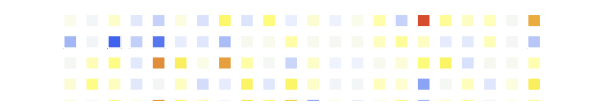

```mathematica
BF=BackFill[T2,S2,Max2,Min2];
bf=Rotate[BF,-1.5708]
```

```mathematica
FrontEdge[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.015],If[array1[[i,j]]==0, White, ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[0],If[array2[[i,j]]>Max2,Black,ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]]}]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows+0.2},{Start-1,Finish+0.2}},AspectRatio->(Finish-Start+1)/Length[Template],ImageSize->600]]
```

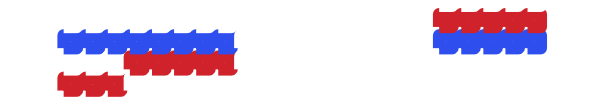

```mathematica
FE=FrontEdge[T2,S2,Max2,Min2];
fe=Rotate[FE,-1.5708]
```

```mathematica
Cutoff[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},(*Get the number of rows and columns from the arrays*){rows,cols}=Dimensions[array1];
(*Create the grid of rectangles with specified edge and fill colors*)grid=Table[Style[Rectangle[{i-0.1,j-0.1},{i-1+spacing+0.1,j-1+spacing+0.1}],EdgeForm[{Thickness[0.015],Opacity[0],If[array1[[i,j]]==0,White,ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]]}],FaceForm[{Opacity[If[Abs[array2[[i,j]]]>Abs[Max2],1,0]],Black}]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows+0.2},{Start-1,Finish+0.2}},AspectRatio->(Finish-Start+1)/Length[Template],ImageSize->600]]
```

```mathematica
CO=Cutoff[T2,S2,Max2,Min2];
```

```mathematica
co=Rotate[CO,-1.5708]
```

-Graphics-

```mathematica
febf=Overlay[{fe,bf}]
```

-Graphics--Graphics-

```mathematica
MainChart=Overlay[{febf,co}]
```

-Graphics--Graphics--Graphics-

```mathematica
L=BarLegend[{"TemperatureMap",{-Abs[h],Abs[h]}},LegendMarkerSize->600]
```

```mathematica
Clocks=Grid[Transpose[{sorted3}],Spacings->{0,1.54}];
```

```mathematica
Export[StringJoin["/Users/nv/Downloads/results/Output/Ein",ToString[GPSDay],"_",ToString[Event],".pdf"],MainChart]
Export[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/Einvtileplot_",ToString[GPSDay],"_",ToString[Event],".PDF"],MainChart]
Export[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/Einvclocks_",ToString[GPSDay],"_",ToString[Event],".PDF"],Clocks]
Export[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/Einvlegend_",ToString[GPSDay],"_",ToString[Event],".PDF"],L]
```

/Users/nv/Downloads/results/Output/Ein16081_2745.pdf

/Users/nv/Downloads/results/16081/Einvtileplot_16081_2745.PDF

/Users/nv/Downloads/results/16081/Einvclocks_16081_2745.PDF

/Users/nv/Downloads/results/16081/Einvlegend_16081_2745.PDF

```mathematica
(*Export["test.pdf",LabeledChart]*)
```

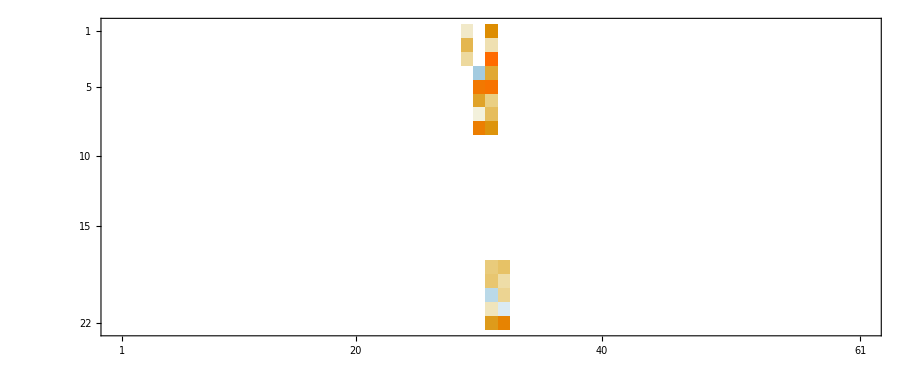

```mathematica
MatrixPlot[Partition[Flatten[T2]*Flatten[S2],61]]
```

```mathematica
Partition[Flatten[T2]*Flatten[S2],61]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0733616 | 0. | 0.50702 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.282046 | 0. | 0.124029 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.146247 | 0. | 0.90206 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.231904 | 0.390045 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.750128 | 0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.399203 | 0.208965 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00804551 | 0.247767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.693153 | 0.473616 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.214888 | 0.24123 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.233129 | 0.133095 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.172068 | 0.167583 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.100332 | -0.0799828 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.433086 | 0.652312 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Total[Flatten[T2]*Flatten[S2]]
```

7.69739

```mathematica
S2//MatrixForm
Max[S2]
Min[S2]
```

(-0.0493724 | -0.0206112 | 0.0493845 | -0.011972 | 0.14349 | 0.198583 | 0.31616 | 0.104358 | -0.071716 | 0.158777 | 0.0941377 | 0.163472 | 0.0656519 | 0.134774 | 0.0931601 | 0.00248535 | -0.15955 | 0.144784 | -0.144006 | -0.129878 | -0.178037 | 0.073027 | 0.191446 | -0.150007 | 0.0233268 | -0.150445 | 0.143242 | 0.0733498 | 0.0733616 | -0.0807509 | -0.50702 | -0.0155839 | 0.0139472 | -0.14642 | -0.243702 | 0.270525 | -0.0812191 | 0.0583189 | 0.268893 | 0.00734892 | -0.166866 | 0.143224 | -0.0450204 | 0.254275 | -0.158459 | -0.213512 | -0.233239 | 0.0524121 | -0.0968955 | 0.0556335 | -0.0759839 | 0.0814658 | -0.234756 | 0.0912861 | -0.0698151 | 0.0515374 | -0.00378192 | -0.0628596 | -0.0787079 | 0.277938 | 0.0603863
-0.153263 | -0.0616799 | -0.166398 | -0.188815 | 0.0850906 | 0.240877 | -0.0986256 | -0.19546 | 0.128415 | -0.385692 | 0.0370417 | -0.0172271 | -0.123648 | 0.156207 | 0.0114689 | 0.0357057 | -0.0764292 | -0.1304 | 0.108208 | 0.0420204 | -0.107802 | 0.143201 | -0.214531 | -0.208125 | -0.0298855 | 0.0864129 | 0.187416 | -0.0913032 | 0.282046 | 0.173085 | -0.124029 | -0.109359 | -0.207455 | -0.108774 | -0.00451915 | -0.116531 | -0.210062 | 0.639126 | -0.310189 | 0.271259 | -0.185284 | -0.073441 | 0.177441 | 0.128491 | -0.158319 | 0.320722 | -0.0728765 | 0.305683 | -0.058557 | -0.0453174 | 0.100345 | -0.320155 | 0.178211 | 0.00159285 | -0.0941235 | 0.231796 | -0.253043 | -0.0243002 | -0.0573271 | -0.123989 | -0.0309283
-0.217798 | -0.0578249 | 0.00365452 | -0.0568009 | -0.0268647 | 0.0652929 | -0.101839 | -0.0452992 | -0.0816847 | -0.406995 | 0.151499 | -0.284302 | 0.0674369 | -0.0977096 | 0.0120067 | -0.0566492 | 0.0857206 | -0.113485 | 0.0436051 | -0.128347 | 0.160798 | 0.049242 | -0.0146827 | 0.151777 | -0.365343 | 0.188728 | -0.383533 | 0.290963 | 0.146247 | 0.282787 | -0.90206 | 0.10705 | -0.179219 | -0.183154 | 0.0818635 | -0.476271 | -0.0576316 | -0.0359486 | 0.42889 | 0.0716057 | 0.282393 | -0.0593548 | 0.169913 | 0.250951 | 0.26224 | -0.17062 | -0.361276 | 0.0950101 | -0.192325 | -0.25175 | 0.0103855 | -0.00571059 | -0.0633341 | 0.195328 | 0.128971 | -0.240735 | -0.17631 | -0.0871654 | 0.255873 | 0.00515348 | -0.170962
0.198674 | -0.159793 | 0.400281 | -0.0336863 | 0.0308793 | 0.130146 | -0.155132 | 0.0631964 | -0.20319 | 0.0193427 | -0.0630629 | -0.0829528 | -0.144086 | -0.17832 | -0.177248 | 0.0197234 | -0.0941208 | -0.401204 | 0.00266863 | 0.428226 | -0.000773401 | -0.132858 | 0.0668755 | -0.00564252 | 0.0399384 | -0.320329 | 0.357158 | 0.0300314 | -0.23907 | -0.231904 | -0.390045 | -0.239373 | -0.401591 | -0.205352 | -0.0556521 | -0.365822 | -0.122131 | 0.0109428 | 0.00384982 | 0.159315 | 0.219792 | -0.0165087 | 0.369283 | -0.0422451 | 0.13364 | -0.149867 | -0.0313911 | -0.489245 | 0.105527 | -0.114416 | -0.0671275 | -0.103523 | -0.125538 | 0.186575 | 0.178806 | -0.120401 | 0.400619 | 0.0452092 | 0.104152 | -0.105521 | 0.222569
0.174869 | -0.104607 | 0.0127896 | -0.0748794 | -0.0240195 | -0.184311 | -0.359602 | 0.1223 | -0.565375 | -0.0418157 | -0.504631 | -0.211118 | -0.150786 | -0.0198205 | -0.0266712 | 0.212039 | 0.167573 | 0.0424345 | 0.104778 | 0.207834 | 0.0616495 | 0.338322 | 0.124908 | 0.256466 | 0.0732875 | 0.34661 | 0.295248 | 0.707606 | -0.0986767 | 0.750128 | -0.8 | -0.379287 | -0.215268 | -0.237397 | -0.432261 | -0.0519353 | -0.24734 | -0.303123 | -0.164387 | 0.198886 | -0.0544579 | 0.105193 | -0.0764066 | 0.450153 | -0.0052107 | 0.0215887 | -0.400894 | -0.0449435 | -0.183556 | -0.239466 | -0.0290556 | -0.175155 | -0.297483 | 0.0824128 | -0.120266 | 0.0149117 | -0.146725 | -0.292892 | -0.0450927 | -0.346522 | 0.307649
-0.108173 | -0.207779 | -0.123592 | -0.0537028 | 0.148361 | -0.195755 | -0.235092 | -0.0255015 | -0.0683673 | 0.0677736 | 0.166215 | -0.0240656 | 0.0769984 | 0.00605881 | -0.020435 | 0.0672258 | 0.180804 | 0.0551669 | 0.225151 | -0.207812 | 0.313892 | -0.18049 | 0.0901056 | 0.248665 | 0.0800956 | -0.0193236 | 0.365419 | 0.351 | 0.145584 | 0.399203 | -0.208965 | 0.0314527 | -0.133081 | -0.114627 | -0.219342 | -0.38667 | 0.13074 | -0.173293 | 0.0282636 | -0.0927669 | 0.00756056 | 0.048705 | -0.006834 | 0.335806 | 0.0289093 | -0.289515 | -0.0754824 | -0.20632 | 0.137687 | 0.164752 | -0.17205 | 0.307517 | -0.0403256 | 0.277591 | 0.0366766 | 0.374982 | 0.229567 | 0.547609 | 0.204415 | -0.0541011 | 0.485192
-0.124684 | 0.265173 | 0.216111 | 0.335584 | 0.221769 | 0.0689662 | -0.172611 | 0.0706415 | -0.452215 | 0.0951232 | -0.0230331 | 0.113748 | -0.0914968 | 0.337681 | 0.0902624 | 0.178298 | 0.214008 | 0.14653 | 0.357549 | 0.105594 | 0.108444 | 0.191874 | 0.106865 | 0.154214 | -0.0224367 | 0.0613358 | -0.109381 | 0.190052 | -0.321616 | 0.00804551 | -0.247767 | -0.284684 | -0.132749 | -0.571354 | -0.180742 | -0.189389 | 0.0340726 | 0.112694 | 0.0372758 | 0.093964 | -0.0593122 | -0.0815756 | -0.132658 | 0.048687 | 0.154604 | -0.306166 | -0.276989 | -0.0216861 | 0.012053 | 0.319286 | -0.0959764 | 0.245156 | 0.206861 | 0.15889 | -0.287055 | 0.301725 | 0.144644 | 0.198019 | 0.157753 | -0.0075387 | 0.0991709
-0.265385 | 0.294278 | -0.0210186 | 0.0539928 | -0.0318339 | 0.119407 | -0.097643 | -0.394666 | -0.506994 | -0.0240821 | 0.117765 | -0.0121112 | -0.154697 | -0.174972 | -0.0947334 | -0.257772 | -0.0991573 | -0.580459 | 0.0292619 | -0.0339711 | 0.267396 | -0.261061 | 0.323265 | -0.136086 | 0.0297465 | 0.177065 | -0.2213 | -0.101744 | -0.211029 | 0.693153 | -0.473616 | 0.350128 | 0.115464 | 0.35942 | 0.104006 | -0.0203392 | -0.301281 | -0.0938207 | 0.215797 | -0.100674 | 0.499939 | -0.669876 | -0.0740403 | -0.117594 | 0.100971 | -0.002511 | -0.132135 | 0.732517 | -0.140118 | 0.446235 | 0.165153 | 0.159708 | 0.279645 | -0.109018 | -0.0896041 | -0.498115 | 0.750419 | -0.263583 | -0.320836 | -0.016941 | -0.151795
0.273877 | -0.0437053 | 0.0497682 | 0.0431346 | 0.264941 | -0.446049 | -0.419386 | 0.216021 | 0.306445 | 0.256907 | 0.207116 | 0.0777918 | 0.212623 | 0.0264075 | -0.0426725 | -0.44302 | -0.167558 | -0.00319959 | 0.00554808 | -0.436777 | 0.21701 | -0.0326912 | 0.0140829 | -0.199406 | 0.127715 | -0.117836 | -0.426462 | 0.443391 | 0.367394 | 0.208935 | -0.0514578 | -0.272558 | 0.0275799 | -0.246802 | -0.164073 | 0.230199 | -0.0486138 | 0.0364167 | 0.311323 | -0.202035 | 0.00939527 | -0.363845 | -0.0942351 | -0.254473 | 0.332704 | -0.327602 | -0.307611 | -0.284962 | -0.0859907 | -0.552618 | -0.111379 | 0.114072 | 0.0855943 | 0.0752608 | -0.0209227 | 0.212487 | 0.0927223 | -0.0759531 | 0.313217 | -0.20993 | -0.137208
0.145188 | -0.00717079 | -0.141713 | -0.0795156 | -0.0221109 | -0.00357229 | -0.0178862 | -0.0914273 | -0.0712181 | -0.276637 | -0.310881 | 0.26829 | -0.0360841 | 0.180363 | 0.20147 | -0.0135587 | 0.206954 | 0.14234 | 0.0979591 | 0.182291 | -0.255548 | -0.0153067 | -0.121894 | 0.108017 | -0.0687911 | 0.10658 | 0.188024 | 0.316658 | -0.24453 | -0.0889091 | -0.034728 | 0.298083 | -0.155472 | -0.89095 | -0.0334182 | 0.0521611 | 0.472152 | -0.288048 | -0.4462 | -0.500369 | -0.123042 | 0.351882 | 0.0153536 | 0.358627 | 0.221501 | 0.0228509 | -0.00540731 | -0.105716 | -0.0502784 | -0.0633261 | 0.181086 | -0.34426 | 0.24134 | -0.272948 | 0.00411503 | 0.120229 | 0.038736 | 0.0114398 | 0.463317 | -0.142679 | 0.380084
0.0537609 | -0.0816689 | 0.247056 | 0.0219997 | 0.0387865 | -0.0841765 | 0.250838 | -0.302961 | 0.0652893 | 0.0570347 | -0.0200318 | 0.305158 | -0.0865404 | -0.00319435 | -0.00326493 | 0.266835 | 0.10724 | 0.124963 | 0.227765 | 0.00233372 | 0.402168 | -0.155707 | 0.399506 | 0.160388 | 0.359996 | -0.137743 | 0.909508 | 0.534775 | 0.360244 | -0.361155 | 0.211273 | -0.195231 | -0.120279 | -0.309811 | -0.522991 | -0.147298 | 0.08096 | -0.311731 | -0.310266 | 0.0337078 | -0.0929237 | -0.0328381 | -0.0343193 | 0.216059 | 0.103932 | -0.16332 | -0.246659 | -0.312368 | -0.19504 | 0.100224 | 0.00213296 | -0.0357003 | -0.100909 | -0.232281 | -0.0463927 | 0.165859 | -0.236942 | 0.696852 | -0.130081 | 0.0903766 | 0.0669335
0.0377197 | -0.00843637 | -0.0890684 | 0.144391 | -0.0340846 | -0.116806 | 0.01419 | 0.0884666 | 0.193582 | -0.0332219 | -0.00475156 | -0.17225 | -0.0946444 | 0.0932199 | 0.165939 | 0.192704 | 0.244535 | 0.0340272 | -0.154797 | 0.0425067 | -0.276673 | -0.242603 | -0.196162 | -0.245128 | -0.0912816 | -0.0581172 | 0.23631 | -0.570136 | 0.108832 | 0.115786 | -0.0481852 | 0.0751999 | 0.133187 | 0.276693 | 0.243225 | -0.0805199 | 0.259559 | -0.187003 | 0.229769 | 0.240693 | -0.0517961 | -0.112251 | 0.00302463 | -0.109395 | -0.0655311 | -0.037977 | -0.0595314 | -0.108183 | 0.171761 | 0.0821611 | 0.0409135 | -0.123505 | -0.00173956 | 0.0395303 | -0.195332 | -0.114543 | -0.00904359 | -0.28474 | -0.312898 | 0.0513894 | 0.0996929
0.0144722 | 0.156415 | -0.128294 | 0.0680374 | 0.193625 | 0.17887 | -0.0311193 | -0.142344 | 0.0697872 | 0.19414 | 0.192188 | -0.0460728 | 0.160971 | -0.0213471 | -0.00527172 | -0.221029 | 0.222568 | 0.273127 | -0.00644377 | 0.00112364 | 0.0843446 | 0.0203138 | 0.174606 | 0.0667494 | 0.00279466 | -0.0240971 | 0.108663 | 0.0206259 | -0.131449 | -0.163274 | -0.0784199 | -0.169243 | -0.10214 | -0.0825243 | 0.0055 | -0.0201733 | 0.154737 | -0.146637 | 0.0453744 | 0.0793648 | -0.411902 | -0.166076 | -0.0974941 | -0.0330358 | -0.019802 | 0.107553 | 0.147245 | -0.0946858 | 0.168362 | 0.241905 | 0.173454 | 0.0569878 | 0.257129 | -0.132072 | 0.13428 | 0.136335 | -0.0259181 | 0.293659 | 0.217285 | 0.00312706 | 0.0876889
-0.131909 | -0.108528 | -0.064661 | -0.148919 | 0.212924 | -0.123776 | -0.0200708 | 0.0900015 | 0.114548 | 0.18363 | 0.206241 | 0.0674293 | 0.139934 | 0.11996 | -0.0103538 | 0.142367 | 0.125914 | 0.560774 | 0.0684223 | 0.116795 | -0.130326 | 0.17595 | -0.262882 | -0.06854 | 0.00676439 | -0.199977 | -0.0483606 | -0.208546 | -0.109537 | -0.169639 | -0.0491336 | -0.0231334 | 0.0264224 | 0.0140927 | 0.199404 | 0.185049 | -0.00677014 | 0.256008 | -0.0293085 | 0.118518 | -0.09809 | -0.0714365 | 0.303787 | -0.0358049 | -0.108874 | 0.0567856 | 0.0618284 | -0.0229984 | 0.291712 | 0.295898 | -0.0957376 | -0.0530634 | -0.180544 | -0.173433 | 0.0716839 | -0.0560352 | -0.105913 | 0.0926732 | 0.262656 | 0.0729105 | 0.0866513
-0.168711 | -0.101764 | 0.155818 | -0.0430753 | 0.00846962 | 0.010276 | -0.0291034 | -0.11182 | 0.0416828 | -0.144916 | 0.0449249 | 0.0101763 | -0.0421802 | -0.349146 | 0.31522 | 0.0447448 | -0.0640553 | 0.275721 | -0.0402723 | -0.207779 | 0.214853 | -0.331738 | -0.0960814 | -0.181271 | 0.0539258 | -0.142861 | -0.16004 | -0.00390212 | 0.151319 | -0.0532357 | 0.146249 | 0.201082 | 0.0692006 | 0.362085 | -0.173357 | -0.228849 | 0.419488 | 0.122363 | 0.0528825 | -0.184294 | -0.492016 | 0.168556 | -0.16238 | -0.167745 | -0.119804 | 0.128599 | -0.35086 | 0.0155567 | 0.10723 | 0.0336615 | 0.0690664 | -0.15225 | -0.0695356 | -0.296069 | -0.0545412 | -0.268621 | -0.579105 | -0.0808381 | 0.0585029 | -0.107574 | -0.203853
-0.191364 | 0.0642802 | -0.254379 | 0.0038937 | -0.261945 | 0.13393 | -0.0414828 | 0.0669507 | 0.19353 | -0.0618677 | -0.137088 | -0.00829262 | -0.0910382 | -0.0710115 | 0.0303119 | -0.147748 | 0.052831 | -0.0456436 | 0.07707 | 0.0220703 | 0.0968831 | -0.152378 | 0.25833 | -0.134264 | 0.0208493 | 0.191423 | 0.106919 | 0.269853 | 0.0904876 | 0.0601981 | 0.237715 | -0.374106 | 0.10421 | -0.021668 | 0.0267532 | 0.218261 | -0.0129517 | -0.30213 | 0.187488 | -0.320772 | -0.27625 | -0.198792 | 0.00961996 | 0.174733 | 0.173585 | -0.324188 | 0.0721665 | -0.11562 | 0.302321 | -0.0068731 | 0.200098 | 0.0941267 | 0.0737111 | 0.161125 | 0.12804 | 0.047195 | 0.0977796 | 0.105314 | -0.0385667 | 0.0246249 | -0.0848775
-0.673072 | -0.388376 | 0.263333 | -0.214486 | -0.793292 | 0.118829 | 0.565828 | -0.559155 | 0.446992 | 0.678914 | 0.174193 | 0.20679 | -0.745918 | 0.413567 | -0.157893 | -0.619784 | -1.38859 | -0.347043 | -0.187033 | 0.247953 | -0.0564397 | -0.193183 | -0.291359 | -1.0261 | -0.0807741 | 0.0633268 | -0.410002 | -0.498817 | -0.590354 | 0.304674 | 0.137753 | 0.914169 | 0.511556 | 0.922568 | 0.216457 | 1.51033 | 0.793434 | 0.510441 | 0.0999782 | -0.768442 | -0.323477 | -0.478429 | -0.929536 | -1.12343 | -0.949046 | 0.410255 | -0.0760217 | -0.432109 | -0.544363 | -1.12539 | -0.624556 | 0.0505876 | 0.172774 | 0.388689 | 0.0377941 | -2.122 | -0.364185 | 0.741627 | -0.179842 | -0.593374 | 0.0900484
0.417352 | -0.245219 | 0.00815125 | 0.181687 | -0.489435 | -0.0523898 | -0.346803 | -0.268748 | 0.0854839 | -0.264308 | -0.0992318 | 0.0163981 | 0.190415 | 0.22485 | 0.187633 | -0.0760358 | 0.535666 | 0.161023 | 0.305978 | 0.141077 | 0.499303 | 0.0124991 | 0.380398 | 0.115802 | -0.0159662 | 0.249983 | -0.0144478 | 0.157035 | -0.0879422 | 0.371907 | -0.214888 | 0.24123 | -0.301162 | -0.197798 | -0.261587 | -0.113265 | -0.273749 | -0.0711349 | -0.173053 | -0.295224 | 0.177558 | 0.0590575 | -0.0770147 | -0.0647414 | 0.205196 | -0.0747157 | -0.327475 | 0.302813 | -0.201317 | -0.198914 | -0.104643 | -0.136306 | -0.0359722 | -0.0259993 | -0.0446862 | 0.538051 | 0.353669 | 0.0623648 | 0.370304 | -0.115032 | 0.0122961
0.226368 | 0.187084 | -0.058582 | -0.119374 | 0.0497125 | -0.166523 | 0.0517795 | -0.0902432 | -0.0306025 | 0.200146 | -0.357234 | -0.109594 | -0.0804546 | -0.0290119 | 0.0515633 | -0.115023 | 0.0115343 | -0.131317 | -0.0303315 | 0.10742 | 0.161384 | 0.115455 | 0.011246 | 0.320212 | -0.129035 | -0.0104306 | 0.25008 | 0.244217 | 0.16305 | -0.292123 | -0.233129 | 0.133095 | 0.0742047 | -0.154009 | -0.166034 | -0.052858 | -0.276827 | -0.128091 | -0.0483821 | -0.131581 | 0.0930051 | -0.177519 | 0.154941 | 0.184264 | 0.361557 | -0.0723422 | 0.0102371 | -0.328428 | -0.0617033 | -0.28253 | 0.0227186 | -0.201859 | 0.119248 | -0.54447 | 0.192064 | -0.0159607 | -0.155983 | -0.173248 | 0.173233 | 0.0950389 | -0.0948807
0.157184 | -0.13256 | 0.0478603 | -0.111326 | 0.0819484 | -0.0192381 | 0.060345 | 0.0751381 | 0.477377 | -0.48297 | 0.72509 | 0.0244268 | -0.270595 | 0.163687 | -0.208333 | -0.0672171 | -0.118536 | -0.0736656 | -0.352694 | 0.119876 | -0.000846804 | 0.0663242 | -0.367625 | 0.0767721 | 0.134202 | 0.255566 | 0.0364029 | -0.101717 | -0.249732 | -0.062796 | 0.172068 | 0.167583 | 0.00145786 | -0.181934 | 0.0742791 | -0.0987859 | -0.0172649 | -0.0163249 | -0.185348 | -0.0561323 | -0.100839 | -0.0739409 | 0.319181 | -0.252292 | 0.323473 | 0.283088 | -0.129158 | 0.356203 | -0.0437292 | 0.0750152 | 0.130453 | -0.298812 | 0.0543083 | -0.0964608 | -0.306413 | 0.0620606 | 0.185665 | 0.236255 | -0.195978 | -0.448768 | 0.310348
0.00791334 | -0.267782 | 0.159697 | -0.122509 | 0.0271389 | 0.262131 | 0.202224 | -0.151925 | -0.413461 | -0.169257 | -0.0194598 | -0.17289 | 0.0860319 | 0.124133 | 0.0229695 | 0.148981 | -0.104895 | 0.0160373 | 0.302917 | 0.135318 | -0.094155 | 0.11537 | -0.159178 | 0.0214741 | 0.018318 | -0.0442181 | -0.106776 | -0.00656077 | 0.0351601 | -0.0569514 | -0.100332 | -0.0799828 | -0.0571344 | 0.138269 | 0.00915989 | 0.0512302 | -0.108088 | -0.0417498 | -0.0675092 | -0.021667 | -0.0911578 | 0.0130203 | 0.183868 | 0.0654219 | 0.187021 | 0.0382514 | -0.0738093 | -0.219025 | -0.0529148 | 0.0964606 | 0.236948 | -0.0144593 | -0.0491192 | -0.205668 | -0.222691 | 0.172171 | -0.027141 | -0.0408186 | 0.181326 | -0.0553035 | 0.0728468
-0.534754 | -0.0885324 | -0.124954 | -0.400678 | 0.0674152 | -0.0804727 | -0.0221455 | 0.244699 | -0.322625 | -0.159363 | 0.0732764 | 0.0398643 | -0.323403 | 0.15747 | -0.11141 | -0.191699 | -0.00683986 | -0.1084 | -0.148021 | -0.132766 | -0.254211 | 0.341036 | -0.40854 | 0.299562 | -0.0456112 | -0.10102 | -0.102433 | 0.236452 | 0.398488 | 0.187975 | -0.433086 | 0.652312 | -0.0816127 | -0.294599 | 0.0935357 | -0.12718 | -0.0476721 | 0.122984 | 0.216332 | 0.118523 | 0.214303 | 0.68779 | -0.174815 | 0.561775 | 0.215566 | -0.209568 | -0.0169743 | -0.0489165 | 0.234077 | 0.111251 | 0.0804831 | 0.327427 | -0.148711 | 0.283667 | -0.0493288 | -0.162664 | 0.0642453 | -0.187064 | 0.128584 | -0.214393 | 0.0885201)

1.51033

-2.122

```mathematica
Mean[Mean[Abs[S2]]]
```

0.17685

```mathematica
Mean[Abs[V]]
```

0.17685

```mathematica
Max[Max[S2],Abs[Min[S2]]]
```

2.122

```mathematica
newArray=Transpose[S2][[Start;;Finish]]
```

{{0.0733616,0.282046,0.146247,-0.23907,-0.0986767,0.145584,-0.321616,-0.211029,0.367394,-0.24453,0.360244,0.108832,-0.131449,-0.109537,0.151319,0.0904876,-0.590354,-0.0879422,0.16305,-0.249732,0.0351601,0.398488},{-0.0807509,0.173085,0.282787,-0.231904,0.750128,0.399203,0.00804551,0.693153,0.208935,-0.0889091,-0.361155,0.115786,-0.163274,-0.169639,-0.0532357,0.0601981,0.304674,0.371907,-0.292123,-0.062796,-0.0569514,0.187975},{-0.50702,-0.124029,-0.90206,-0.390045,-0.8,-0.208965,-0.247767,-0.473616,-0.0514578,-0.034728,0.211273,-0.0481852,-0.0784199,-0.0491336,0.146249,0.237715,0.137753,-0.214888,-0.233129,0.172068,-0.100332,-0.433086},{-0.0155839,-0.109359,0.10705,-0.239373,-0.379287,0.0314527,-0.284684,0.350128,-0.272558,0.298083,-0.195231,0.0751999,-0.169243,-0.0231334,0.201082,-0.374106,0.914169,0.24123,0.133095,0.167583,-0.0799828,0.652312}}

```mathematica
Max[Max[newArray],Abs[Min[newArray]]]
```

0.914169

```mathematica
Mean[Abs[Flatten[newArray]]]
```

0.236802

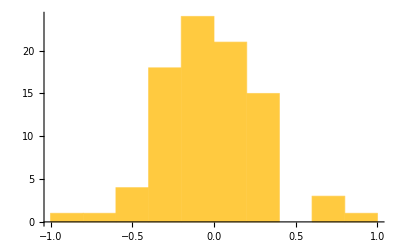

```mathematica
Histogram[Flatten[newArray]]
```